```mathematica
x0=Pi/2;
vx0=-1;
y0=0;
vy0=0;

tf=15;

sol=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==-Sin[y[t]-x[t]],x'[0]==vx0,y'[0]==vy0,x[0]==x0,y[0]==y0},{x,y},{t,0,tf}];

s1= x  /. First@sol;
s2= y /. First@sol;

hoop =ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
colors={RGBColor[0.394, 0.394, 0.394],RGBColor[0.668, 0.668, 0.668]};

Animate[Show[hoop,ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{colors[[1]],PointSize[.1],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{colors[[2]],PointSize[.1],Point[{Cos[s2[t]],Sin[s2[t]]}]}]],{t,0,tf}]
```

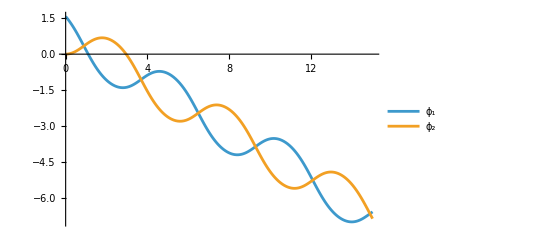

```mathematica
Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All]]
```